```mathematica
By Le Chen.
Crated on Wed 13 Apr 2022 10:17:05 AM CDT
```

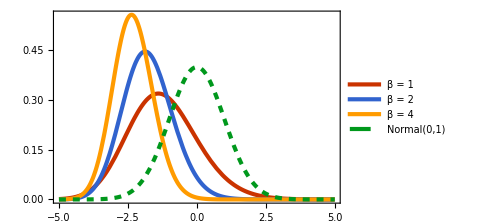

Trace-Widom.png

```mathematica
f=Plot[{Table[PDF[TracyWidomDistribution[β],x],{β,{1,2,4}}],PDF[NormalDistribution[0,1],x]}//Evaluate,{x,-5,5},Filling->{Axis,Axis,Axis,None},PlotLegends->Placed[{"β = 1","β = 2","β = 4","Normal(0,1)"},Above],ImageSize->Medium,PlotTheme->"Web",PlotStyle->{Thick,Thick,Thick,Dashed}]
Export["Trace-Widom.png",f]
```

```mathematica
Table[PDF[TracyWidomDistribution[β],x],{β,{1,2,4}}]
```

```mathematica
{PDF[TracyWidomDistribution[1],x],PDF[TracyWidomDistribution[2],x],PDF[TracyWidomDistribution[4],x],PDF[NormalDistribution[0,1],x]}
```

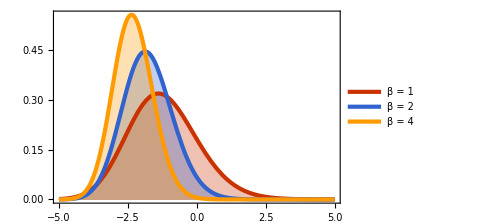

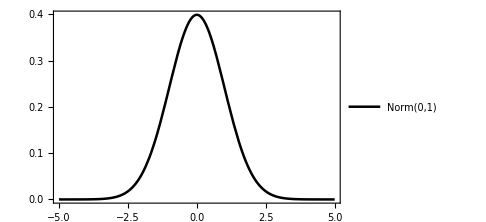

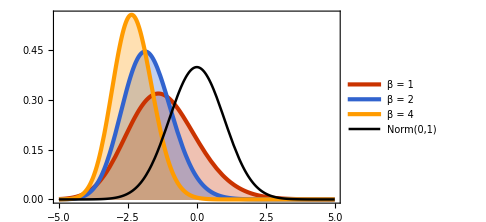

Trace-Widom.png

-Graphics-

```mathematica
f1=Plot[{Table[PDF[TracyWidomDistribution[β],x],{β,{1,2,4}}]}//Evaluate,{x,-5,5},Filling->Axis,PlotLegends->Placed[{"β = 1","β = 2","β = 4"},Above],ImageSize->Medium,PlotTheme->"Web",PlotStyle->{Thick,Thick,Thick,Dashed}]
f2=Plot[{PDF[NormalDistribution[0,1],x]}//Evaluate,{x,-5,5},Filling->None,PlotLegends->Placed[{"Norm(0,1)"},Above],ImageSize->Medium,PlotTheme->"Web",PlotStyle->{Thickness[0.005],Black}]
ffinal = Show[f1,f2]
Export["Trace-Widom.png",ffinal]
```

```mathematica
Show[f1,f2]
```

-Graphics-